# In-Class Demo (01-25-2022)

## Systems of First-Order ODEs

Consider the system given by 

ẋ = f(x,y)        where   f(x,y) = 2x + 4x y
ẏ = g(x,y)      where   g(x,y)= 6xy - 8y

We would like to (1) conduct local analysis, and (2) graph the phase plane to validate our local analysis conclusions.

### A First Glimpse at the Phase Plane

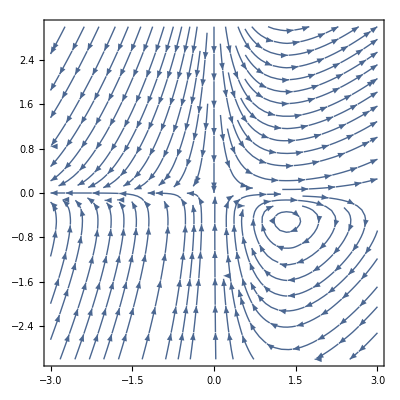

```mathematica
StreamPlot[{2x +4 x y,6 x y - 8y},{x,-3,3},{y,-3,3}]
```

### Local Analysis

```mathematica
f[x_,y_]=2x +4 x y;
g[x_,y_] = 6x y -8 y;
```

#### Find the Equilibrium Points

```mathematica
eqPts = Solve[{f[x,y]==0,g[x,y]==0},{x,y}]
```

{{x→4/3,y→-1/2},{x→0,y→0}}

#### Define the Jacobian “Df”

```mathematica
Df = Grad[{f[x,y],g[x,y]},{x,y}]
Df//MatrixForm
```

{{2+4 y,4 x},{6 y,-8+6 x}}

(2+4 y | 4 x
6 y | -8+6 x)

#### At p_2 = (x_2^*,y_2^*) = (0,0)

```mathematica
A2=Df/.eqPts[[2]]
```

{{2,0},{0,-8}}

```mathematica
A2//MatrixForm
```

(2 | 0
0 | -8)

```mathematica
Eigensystem[A2]//MatrixForm
```

(-8 | 2
{0,1} | {1,0})

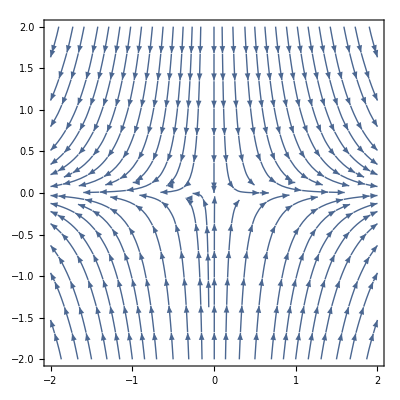

```mathematica
StreamPlot[A2.{{x},{y}},{x,-2,2},{y,-2,2}]
```

#### At p_1 = (x_1^*,y_1^*) = (4/3,-1/2)

```mathematica
A1=Df/.eqPts[[1]]
```

{{0,16/3},{-3,0}}

```mathematica
A1//MatrixForm
```

(0 | 16/3
-3 | 0)

```mathematica
Eigensystem[A1]//MatrixForm
```

(4 ⅈ | -4 ⅈ
{-(4 ⅈ)/3,1} | {(4 ⅈ)/3,1})

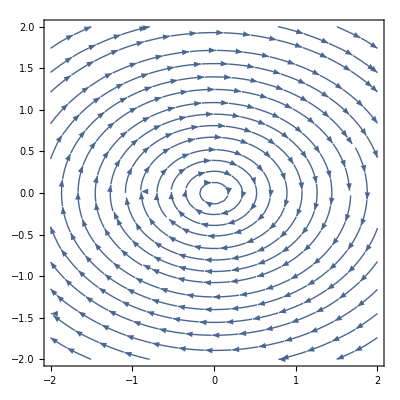

```mathematica
StreamPlot[A1.{{x},{y}},{x,-2,2},{y,-2,2}]
```

```mathematica
Eigensystem[A1]//MatrixForm
```

(4 ⅈ | -4 ⅈ
{-(4 ⅈ)/3,1} | {(4 ⅈ)/3,1})

## Comparing with the Direction Field

```mathematica
For[j=1,j≤Length[eqPts],j++,
esys = Eigensystem[Df/.eqPts[[j]]];
Subscript[evPlots, j]=ParametricPlot[esys[[2]]*s + Table[{x,y}/.eqPts[[j]] ,{k,1,2}],{s,-1,1},
PlotStyle->{Red, Thickness->.015},
RegionFunction->Function[{u,v,vx,vy,n},(((u-x)^2+(v -y)^2)/.eqPts[[j]])<.1]]];
EVPlot = Show[Table[Subscript[evPlots, j],{j,1,Length[eqPts]}]];
eqPtsPlot = ListPlot[{x,y}/.eqPts,
PlotMarkers->{Automatic,Scaled[.04]},
PlotStyle->Black];
```

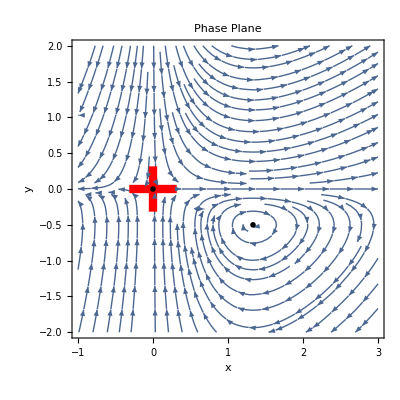

```mathematica
pplanePlot = StreamPlot[{f[x,y],g[x,y]},{x,-1,3},{y,-2,2},
FrameLabel->{"x","y"},
PlotLabel->"Phase Plane"];

phasePlaneFinal=Show[pplanePlot,EVPlot,eqPtsPlot]
```

```mathematica
sysSol=NDSolve[{x'[t]==f[x[t],y[t]],y'[t]==g[x[t],y[t]],x[0]==1/2,y[0]==-1/2},{x[t],y[t]},{t,0,5}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

```mathematica
Plot[Evaluate[{x[t],y[t]}/.sysSol],{t,0,5},PlotLabels->{"x(t)","y(t)"}]
```

-Graphics-

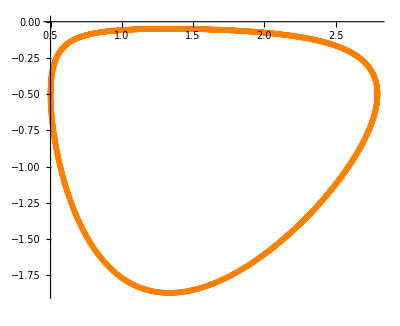

```mathematica
parPlot=ParametricPlot[Evaluate[{x[t],y[t]}/.sysSol],{t,0,5},
PlotStyle-> {Thickness[.01],Orange}]
```

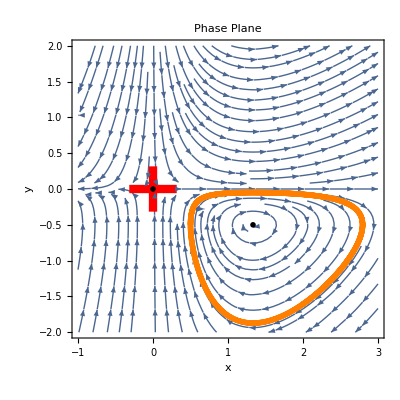

```mathematica
Show[phasePlaneFinal,parPlot]
```